# Exercises

### Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
ClearAll["Global`*"]
y ={0, 0.1, 0.2, 0.4, 0.8};
f[x_]=x*Exp[-x]+x(1-x)
```

ⅇ^-x x+(1-x) x

```mathematica
For[i = 1, i<6, i++,Print[f[y[[i]]]]]
```

0

0.180484

0.323746

0.508128

0.519463

### Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

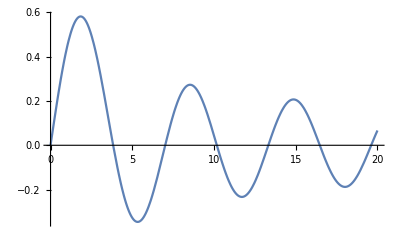

```mathematica
BesselJ1[x_]:=BesselJ[1,x]
Plot[BesselJ1[x],{x,0,20}]
```

```mathematica
roots=x/. NSolve[BesselJ1[x]==0&&0<x<13,x,3]
```

{3.83,7.02,10.2}

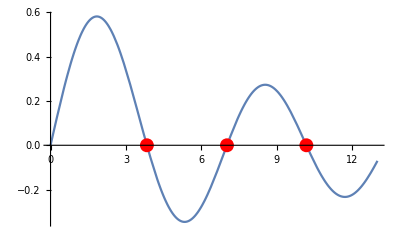

```mathematica
Plot[BesselJ1[x],{x,0,13},Epilog->{Red,PointSize[0.025],Point[{#,0}&/@roots]}]
```

### Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
f[x_]=Sin[x]*Exp[-x]
g = Integrate[f[x],x]
h = Simplify[D[g,x]]
```

ⅇ^-x Sin[x]

-1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]

### Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
f[x_]=Exp[-ArcTan[x]]
Series[f[x], {x, ∞, 5}]
Series[f[x], {x, 0, 5}]
```

ⅇ^(-ArcTan[x])

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+ⅇ^(-π/2)/(24 x^5)+O[1/x]^6

1-x+x^2/2+x^3/6-(7 x^4)/24-x^5/24+O[x]^6

### Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them. y’’(x) - x, y(x) = 0, y(0) = 1, y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
ClearAll["Global`*"]
g=y''[x]-x y[x]==0
init={y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]};
```

-x y[x]+y''[x]==0

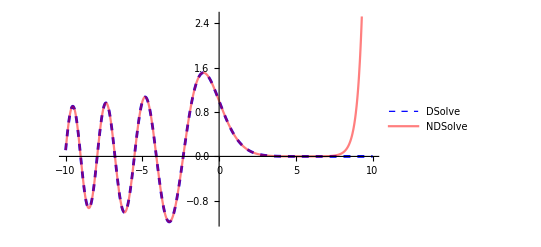

```mathematica
dsolve = DSolve[{g, init},y[x],x];
ndsolve = NDSolve[{g, init},y[x],{x, -10, 10}];
Plot[
Evaluate[{y[x]/. dsolve,y[x]/. ndsolve}],{x,-10,10},
PlotStyle->{{Dashed,Blue, Thickness[0.005]},{Red, Opacity[0.5]}},
PlotLegends->{"DSolve","NDSolve"}
]
```